```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
g[x_]:=Quiet[NIntegrate[(2 p)/(p^2+1)Sinc[p x],{p,0,∞}]];
```

## Fundamental Solution

```mathematica
DSolve[f''[x]-1/x f'[x]-x^3 f[x]==0,f[x],x]
```

{{f[x]→(x BesselI[-2/5,(2 x^(5/2))/5] C[1] Gamma[3/5])/5^(2/5)+(-1/5)^(2/5) x BesselI[2/5,(2 x^(5/2))/5] C[2] Gamma[7/5]}}

```mathematica
u1[x_]:=x BesselI[-2/5,(2 x^(5/2))/5];
```

```mathematica
u1''[x]-1/x u1'[x]-x^3 u1[x]//FullSimplify
```

0

```mathematica
u2[x_]:=x BesselI[2/5,(2 x^(5/2))/5];
```

```mathematica
u2''[x]-1/x u2'[x]-x^3 u2[x]//FullSimplify
```

0

## Homogeneous Solution with BCs

### BC1 : y'[0] = y[0]=0

```mathematica
D[u1[x],x]
```

BesselI[-2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-7/5,(2 x^(5/2))/5]+BesselI[3/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u1[x],x],x->0]
```

0

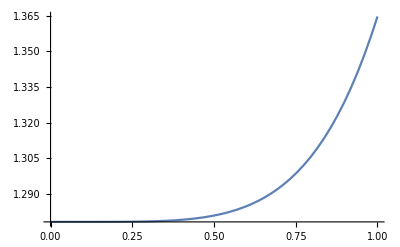

```mathematica
Plot[u1[x],{x,0,1},PlotRange->All]
```

```mathematica
Limit[u1[x],x->0]
```

5^(2/5)/Gamma[3/5]

```mathematica
D[u2[x],x]
```

BesselI[2/5,(2 x^(5/2))/5]+1/2 x^(5/2) (BesselI[-3/5,(2 x^(5/2))/5]+BesselI[7/5,(2 x^(5/2))/5])

```mathematica
Limit[D[u2[x],x],x->0]
```

0

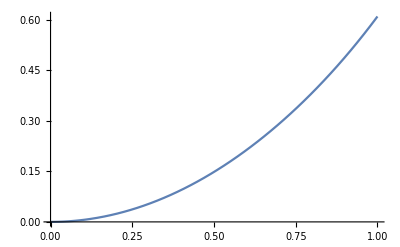

```mathematica
Plot[u2[x],{x,0,1}]
```

```mathematica
u2[0]
```

0

```mathematica
y1[x_]:=u2[x];
```

### BC2 : y'[∞] = 0

```mathematica
Limit[D[u1[x]-u2[x],x],x->∞]
```

0

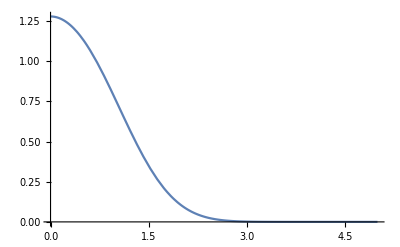

```mathematica
Plot[u1[x]-u2[x],{x,0,5},PlotRange->All]
```

```mathematica
y2[x_]:=u1[x]-u2[x];
```

## Construction of Wronskian

```mathematica
D[y2[x],x]y1[x]-y2[x]D[y1[x],x]//FullSimplify
```

-(5 √(1/2 (5+√5)) x)/(2 π)

```mathematica
W[x_]:=-(5 √(1/2 (5+√5)) x)/(2 π);
```

## Construction of Inhomogeneous Solution

```mathematica
y[x_]:=y2[x]Quiet[NIntegrate[y1[s]/W[s] s^3 g[s],{s,0,x}]]+y1[x]Quiet[NIntegrate[y2[s]/W[s] s^3 g[s],{s,x,∞}]];
```

```mathematica
yTab=Table[{i,0},{i,0.1,10,0.1}];
SetSharedVariable[yTab];
```

```mathematica
ParallelDo[yTab[[i,2]]=y[yTab[[i,1]]],{i,1,Length[yTab]}]
```

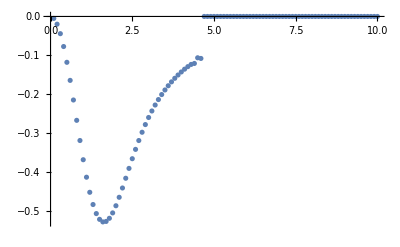

```mathematica
ListPlot[yTab]
```

```mathematica
yInter=Interpolation[yTab[[;;44]]];
```

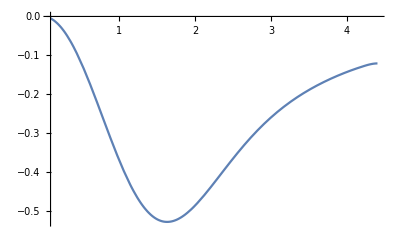

```mathematica
Plot[yInter[x],{x,0.1,4.4}]
```

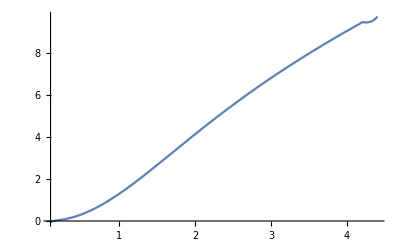

```mathematica
Plot[yInter''[x]-1/x yInter'[x]-x^3 yInter[x],{x,0.1,4.4}]
```

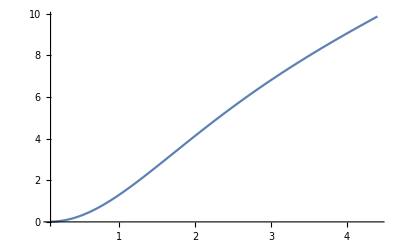

```mathematica
Plot[x^3 g[x],{x,0.1,4.4}]
```

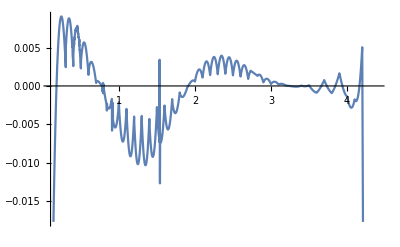

```mathematica
Plot[yInter''[x]-1/x yInter'[x]-x^3 yInter[x]-x^3 g[x],{x,0.1,4.4}]
```